Defining STA Solutions

```mathematica
bsta[t_]=c0+c1 t+c2 t^2+c3 t^3+c4 t^4+c5 t^5
```

c0+c1 t+c2 t^2+c3 t^3+c4 t^4+c5 t^5

```mathematica
solsta = Solve[{bsta[0]==1,bsta'[0]==0,bsta''[0]==0,bsta[tf]==gam,bsta'[tf]==0,bsta''[tf]== 0},{c0,c1,c2,c3,c4,c5}]
```

{{c0→1,c1→0,c2→0,c3→(10 (-1+gam))/tf^3,c4→-(15 (-1+gam))/tf^4,c5→(6 (-1+gam))/tf^5}}

```mathematica
bsta[t_]=bsta[t]/.solsta[[1]]
```

1+(6 (-1+gam) t^5)/tf^5-(15 (-1+gam) t^4)/tf^4+(10 (-1+gam) t^3)/tf^3

```mathematica
omsta2[t_]= ((omsta0^2)/(bsta[t]^4)- (bsta''[t])/bsta[t])//FullSimplify
```

(omsta0^2 tf^20)/((6 (-1+gam) t^5-15 (-1+gam) t^4 tf+10 (-1+gam) t^3 tf^2+tf^5)^4)-(60 (-1+gam) t (2 t^2-3 t tf+tf^2))/(6 (-1+gam) t^5-15 (-1+gam) t^4 tf+10 (-1+gam) t^3 tf^2+tf^5)

Defining Omega

```mathematica
deltaom[t_]= c0 +c1*t+c2*t^2+c3*t^3
```

c0+c1 t+c2 t^2+c3 t^3

```mathematica
sol=Solve[{deltaom[0]== 0,deltaom[tf]== 0,deltaom[tf/3]==a1,deltaom[2tf/3]==a2}, {c0, c1, c2,c3}]
```

{{c0→0,c1→(9 (2 a1-a2))/(2 tf),c2→-(9 (5 a1-4 a2))/(2 tf^2),c3→(27 (a1-a2))/(2 tf^3)}}

```mathematica
deltaomx[t_]=deltaom[t]/.sol[[1]]
```

(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)

```mathematica
om2[t_]=omsta2[t]*(1+deltaomx[t])
```

(1+(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)) ((omsta0^2 tf^20)/((6 (-1+gam) t^5-15 (-1+gam) t^4 tf+10 (-1+gam) t^3 tf^2+tf^5)^4)-(60 (-1+gam) t (2 t^2-3 t tf+tf^2))/(6 (-1+gam) t^5-15 (-1+gam) t^4 tf+10 (-1+gam) t^3 tf^2+tf^5))

Defining Fidelities

```mathematica
eq=b''[t] == (om0^2)/(b[t]^3)- om2[t]*b[t]  
gam  = (om0/omf)^0.5
Fid[bf_,bfdot_]= ((4*om0^2*bf^2*gam^2)/((om0^2*(gam^2+bf^2)^2)+(bfdot*bf*gam^2)^2))^0.5
```

b''[t]==om0^2/b[t]^3-(1+(27 (a1-a2) t^3)/(2 tf^3)-(9 (5 a1-4 a2) t^2)/(2 tf^2)+(9 (2 a1-a2) t)/(2 tf)) ((omsta0^2 tf^20)/((6 (-1+gam) t^5-15 (-1+gam) t^4 tf+10 (-1+gam) t^3 tf^2+tf^5)^4)-(60 (-1+gam) t (2 t^2-3 t tf+tf^2))/(6 (-1+gam) t^5-15 (-1+gam) t^4 tf+10 (-1+gam) t^3 tf^2+tf^5)) b[t]

(om0/omf)^0.5

2. ((bf^2 om0^2 (om0/omf)^1.)/(om0^2 (bf^2+(om0/omf)^1.)^2+bf^2 bfdot^2 (om0/omf)^2.))^0.5

```mathematica
gam
```

(om0/omf)^0.5

```mathematica
om0=1
omsta0 =om0
omf=0.1
tf=10
```

1

1

0.1

10

```mathematica
a1=0.1
a2=0.1
```

0.1

0.1

```mathematica
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fid[bsol[tf],bsol'[tf]]
```

0.998499

Calculating Fidelities from List of a1 & a2 Values

```mathematica
list1=Flatten[Table[{a1,a2},{a1,-0.5,0.5,0.05},{a2,-0.5,0.5,0.05}],1]
```

{{-0.5,-0.5},{-0.5,-0.45},{-0.5,-0.4},{-0.5,-0.35},{-0.5,-0.3},{-0.5,-0.25},{-0.5,-0.2},{-0.5,-0.15},{-0.5,-0.1},{-0.5,-0.05},{-0.5,0.},{-0.5,0.05},{-0.5,0.1},{-0.5,0.15},{-0.5,0.2},{-0.5,0.25},{-0.5,0.3},{-0.5,0.35},{-0.5,0.4},{-0.5,0.45},{-0.5,0.5},{-0.45,-0.5},{-0.45,-0.45},{-0.45,-0.4},{-0.45,-0.35},{-0.45,-0.3},{-0.45,-0.25},{-0.45,-0.2},{-0.45,-0.15},{-0.45,-0.1},{-0.45,-0.05},{-0.45,0.},{-0.45,0.05},{-0.45,0.1},{-0.45,0.15},{-0.45,0.2},{-0.45,0.25},{-0.45,0.3},{-0.45,0.35},{-0.45,0.4},{-0.45,0.45},{-0.45,0.5},{-0.4,-0.5},{-0.4,-0.45},{-0.4,-0.4},{-0.4,-0.35},{-0.4,-0.3},{-0.4,-0.25},{-0.4,-0.2},{-0.4,-0.15},{-0.4,-0.1},{-0.4,-0.05},{-0.4,0.},{-0.4,0.05},{-0.4,0.1},{-0.4,0.15},{-0.4,0.2},{-0.4,0.25},{-0.4,0.3},{-0.4,0.35},{-0.4,0.4},{-0.4,0.45},{-0.4,0.5},{-0.35,-0.5},{-0.35,-0.45},{-0.35,-0.4},{-0.35,-0.35},{-0.35,-0.3},{-0.35,-0.25},{-0.35,-0.2},{-0.35,-0.15},{-0.35,-0.1},{-0.35,-0.05},{-0.35,0.},{-0.35,0.05},{-0.35,0.1},{-0.35,0.15},{-0.35,0.2},{-0.35,0.25},{-0.35,0.3},{-0.35,0.35},{-0.35,0.4},{-0.35,0.45},{-0.35,0.5},{-0.3,-0.5},{-0.3,-0.45},{-0.3,-0.4},{-0.3,-0.35},{-0.3,-0.3},{-0.3,-0.25},{-0.3,-0.2},{-0.3,-0.15},{-0.3,-0.1},{-0.3,-0.05},{-0.3,0.},{-0.3,0.05},{-0.3,0.1},{-0.3,0.15},{-0.3,0.2},{-0.3,0.25},{-0.3,0.3},{-0.3,0.35},{-0.3,0.4},{-0.3,0.45},{-0.3,0.5},{-0.25,-0.5},{-0.25,-0.45},{-0.25,-0.4},{-0.25,-0.35},{-0.25,-0.3},{-0.25,-0.25},{-0.25,-0.2},{-0.25,-0.15},{-0.25,-0.1},{-0.25,-0.05},{-0.25,0.},{-0.25,0.05},{-0.25,0.1},{-0.25,0.15},{-0.25,0.2},{-0.25,0.25},{-0.25,0.3},{-0.25,0.35},{-0.25,0.4},{-0.25,0.45},{-0.25,0.5},{-0.2,-0.5},{-0.2,-0.45},{-0.2,-0.4},{-0.2,-0.35},{-0.2,-0.3},{-0.2,-0.25},{-0.2,-0.2},{-0.2,-0.15},{-0.2,-0.1},{-0.2,-0.05},{-0.2,0.},{-0.2,0.05},{-0.2,0.1},{-0.2,0.15},{-0.2,0.2},{-0.2,0.25},{-0.2,0.3},{-0.2,0.35},{-0.2,0.4},{-0.2,0.45},{-0.2,0.5},{-0.15,-0.5},{-0.15,-0.45},{-0.15,-0.4},{-0.15,-0.35},{-0.15,-0.3},{-0.15,-0.25},{-0.15,-0.2},{-0.15,-0.15},{-0.15,-0.1},{-0.15,-0.05},{-0.15,0.},{-0.15,0.05},{-0.15,0.1},{-0.15,0.15},{-0.15,0.2},{-0.15,0.25},{-0.15,0.3},{-0.15,0.35},{-0.15,0.4},{-0.15,0.45},{-0.15,0.5},{-0.1,-0.5},{-0.1,-0.45},{-0.1,-0.4},{-0.1,-0.35},{-0.1,-0.3},{-0.1,-0.25},{-0.1,-0.2},{-0.1,-0.15},{-0.1,-0.1},{-0.1,-0.05},{-0.1,0.},{-0.1,0.05},{-0.1,0.1},{-0.1,0.15},{-0.1,0.2},{-0.1,0.25},{-0.1,0.3},{-0.1,0.35},{-0.1,0.4},{-0.1,0.45},{-0.1,0.5},{-0.05,-0.5},{-0.05,-0.45},{-0.05,-0.4},{-0.05,-0.35},{-0.05,-0.3},{-0.05,-0.25},{-0.05,-0.2},{-0.05,-0.15},{-0.05,-0.1},{-0.05,-0.05},{-0.05,0.},{-0.05,0.05},{-0.05,0.1},{-0.05,0.15},{-0.05,0.2},{-0.05,0.25},{-0.05,0.3},{-0.05,0.35},{-0.05,0.4},{-0.05,0.45},{-0.05,0.5},{0.,-0.5},{0.,-0.45},{0.,-0.4},{0.,-0.35},{0.,-0.3},{0.,-0.25},{0.,-0.2},{0.,-0.15},{0.,-0.1},{0.,-0.05},{0.,0.},{0.,0.05},{0.,0.1},{0.,0.15},{0.,0.2},{0.,0.25},{0.,0.3},{0.,0.35},{0.,0.4},{0.,0.45},{0.,0.5},{0.05,-0.5},{0.05,-0.45},{0.05,-0.4},{0.05,-0.35},{0.05,-0.3},{0.05,-0.25},{0.05,-0.2},{0.05,-0.15},{0.05,-0.1},{0.05,-0.05},{0.05,0.},{0.05,0.05},{0.05,0.1},{0.05,0.15},{0.05,0.2},{0.05,0.25},{0.05,0.3},{0.05,0.35},{0.05,0.4},{0.05,0.45},{0.05,0.5},{0.1,-0.5},{0.1,-0.45},{0.1,-0.4},{0.1,-0.35},{0.1,-0.3},{0.1,-0.25},{0.1,-0.2},{0.1,-0.15},{0.1,-0.1},{0.1,-0.05},{0.1,0.},{0.1,0.05},{0.1,0.1},{0.1,0.15},{0.1,0.2},{0.1,0.25},{0.1,0.3},{0.1,0.35},{0.1,0.4},{0.1,0.45},{0.1,0.5},{0.15,-0.5},{0.15,-0.45},{0.15,-0.4},{0.15,-0.35},{0.15,-0.3},{0.15,-0.25},{0.15,-0.2},{0.15,-0.15},{0.15,-0.1},{0.15,-0.05},{0.15,0.},{0.15,0.05},{0.15,0.1},{0.15,0.15},{0.15,0.2},{0.15,0.25},{0.15,0.3},{0.15,0.35},{0.15,0.4},{0.15,0.45},{0.15,0.5},{0.2,-0.5},{0.2,-0.45},{0.2,-0.4},{0.2,-0.35},{0.2,-0.3},{0.2,-0.25},{0.2,-0.2},{0.2,-0.15},{0.2,-0.1},{0.2,-0.05},{0.2,0.},{0.2,0.05},{0.2,0.1},{0.2,0.15},{0.2,0.2},{0.2,0.25},{0.2,0.3},{0.2,0.35},{0.2,0.4},{0.2,0.45},{0.2,0.5},{0.25,-0.5},{0.25,-0.45},{0.25,-0.4},{0.25,-0.35},{0.25,-0.3},{0.25,-0.25},{0.25,-0.2},{0.25,-0.15},{0.25,-0.1},{0.25,-0.05},{0.25,0.},{0.25,0.05},{0.25,0.1},{0.25,0.15},{0.25,0.2},{0.25,0.25},{0.25,0.3},{0.25,0.35},{0.25,0.4},{0.25,0.45},{0.25,0.5},{0.3,-0.5},{0.3,-0.45},{0.3,-0.4},{0.3,-0.35},{0.3,-0.3},{0.3,-0.25},{0.3,-0.2},{0.3,-0.15},{0.3,-0.1},{0.3,-0.05},{0.3,0.},{0.3,0.05},{0.3,0.1},{0.3,0.15},{0.3,0.2},{0.3,0.25},{0.3,0.3},{0.3,0.35},{0.3,0.4},{0.3,0.45},{0.3,0.5},{0.35,-0.5},{0.35,-0.45},{0.35,-0.4},{0.35,-0.35},{0.35,-0.3},{0.35,-0.25},{0.35,-0.2},{0.35,-0.15},{0.35,-0.1},{0.35,-0.05},{0.35,0.},{0.35,0.05},{0.35,0.1},{0.35,0.15},{0.35,0.2},{0.35,0.25},{0.35,0.3},{0.35,0.35},{0.35,0.4},{0.35,0.45},{0.35,0.5},{0.4,-0.5},{0.4,-0.45},{0.4,-0.4},{0.4,-0.35},{0.4,-0.3},{0.4,-0.25},{0.4,-0.2},{0.4,-0.15},{0.4,-0.1},{0.4,-0.05},{0.4,0.},{0.4,0.05},{0.4,0.1},{0.4,0.15},{0.4,0.2},{0.4,0.25},{0.4,0.3},{0.4,0.35},{0.4,0.4},{0.4,0.45},{0.4,0.5},{0.45,-0.5},{0.45,-0.45},{0.45,-0.4},{0.45,-0.35},{0.45,-0.3},{0.45,-0.25},{0.45,-0.2},{0.45,-0.15},{0.45,-0.1},{0.45,-0.05},{0.45,0.},{0.45,0.05},{0.45,0.1},{0.45,0.15},{0.45,0.2},{0.45,0.25},{0.45,0.3},{0.45,0.35},{0.45,0.4},{0.45,0.45},{0.45,0.5},{0.5,-0.5},{0.5,-0.45},{0.5,-0.4},{0.5,-0.35},{0.5,-0.3},{0.5,-0.25},{0.5,-0.2},{0.5,-0.15},{0.5,-0.1},{0.5,-0.05},{0.5,0.},{0.5,0.05},{0.5,0.1},{0.5,0.15},{0.5,0.2},{0.5,0.25},{0.5,0.3},{0.5,0.35},{0.5,0.4},{0.5,0.45},{0.5,0.5}}

```mathematica
Fidtable2:=
Module[{},
Table[{list1[[nr]][[1]],list1[[nr]][[2]],
a1=list1[[nr]][[1]];
a2=list1[[nr]][[2]];
om0= 1;
omsta0=om0;
omf=0.1;
tf=0.1;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fid[bsol[tf],bsol'[tf]]},{nr,1,Length[list1]}]
]
```

```mathematica
result=Fidtable2
```

{{-0.5,-0.5,0.134997},{-0.5,-0.45,0.194536},{-0.5,-0.4,0.336405},{-0.5,-0.35,0.835328},{-0.5,-0.3,0.529938},{-0.5,-0.25,0.261816},{-0.5,-0.2,0.171735},{-0.5,-0.15,0.128114},{-0.5,-0.1,0.102553},{-0.5,-0.05,0.085804},{-0.5,0.,0.0739965},{-0.5,0.05,0.065234},{-0.5,0.1,0.0584789},{-0.5,0.15,0.0531167},{-0.5,0.2,0.0487602},{-0.5,0.25,0.0451536},{-0.5,0.3,0.042121},{-0.5,0.35,0.0395377},{-0.5,0.4,0.0373127},{-0.5,0.45,0.0353779},{-0.5,0.5,0.0336816},{-0.45,-0.5,0.106297},{-0.45,-0.45,0.142169},{-0.45,-0.4,0.211426},{-0.45,-0.35,0.393103},{-0.45,-0.3,0.961438},{-0.45,-0.25,0.425197},{-0.45,-0.2,0.228392},{-0.45,-0.15,0.155466},{-0.45,-0.1,0.118232},{-0.45,-0.05,0.09575},{-0.45,0.,0.080733},{-0.45,0.05,0.0700059},{-0.45,0.1,0.0619676},{-0.45,0.15,0.0557249},{-0.45,0.2,0.0507404},{-0.45,0.25,0.0466717},{-0.45,0.3,0.0432901},{-0.45,0.35,0.0404374},{-0.45,0.4,0.0380006},{-0.45,0.45,0.0358965},{-0.45,0.5,0.034063},{-0.4,-0.5,0.0871688},{-0.4,-0.45,0.111142},{-0.4,-0.4,0.151885},{-0.4,-0.35,0.235536},{-0.4,-0.3,0.485152},{-0.4,-0.25,0.875576},{-0.4,-0.2,0.342928},{-0.4,-0.15,0.199287},{-0.4,-0.1,0.140458},{-0.4,-0.05,0.108844},{-0.4,0.,0.0891782},{-0.4,0.05,0.0757859},{-0.4,0.1,0.0660887},{-0.4,0.15,0.0587489},{-0.4,0.2,0.0530044},{-0.4,0.25,0.0483896},{-0.4,0.3,0.0446039},{-0.4,0.35,0.0414445},{-0.4,0.4,0.0387699},{-0.4,0.45,0.0364783},{-0.4,0.5,0.0344945},{-0.35,-0.5,0.0735346},{-0.35,-0.45,0.0906995},{-0.35,-0.4,0.117512},{-0.35,-0.35,0.165081},{-0.35,-0.3,0.271028},{-0.35,-0.25,0.643374},{-0.35,-0.2,0.649626},{-0.35,-0.15,0.27987},{-0.35,-0.1,0.174279},{-0.35,-0.05,0.126817},{-0.35,0.,0.100052},{-0.35,0.05,0.0829151},{-0.35,0.1,0.071019},{-0.35,0.15,0.0622868},{-0.35,0.2,0.0556098},{-0.35,0.25,0.0503426},{-0.35,0.3,0.0460844},{-0.35,0.35,0.0425731},{-0.35,0.4,0.0396301},{-0.35,0.45,0.0371296},{-0.35,0.5,0.0349805},{-0.3,-0.5,0.0633382},{-0.3,-0.45,0.0762444},{-0.3,-0.4,0.0952365},{-0.3,-0.35,0.12588},{-0.3,-0.3,0.183316},{-0.3,-0.25,0.326156},{-0.3,-0.2,0.890885},{-0.3,-0.15,0.466989},{-0.3,-0.1,0.231553},{-0.3,-0.05,0.152936},{-0.3,0.,0.114544},{-0.3,0.05,0.0919077},{-0.3,0.1,0.0770086},{-0.3,0.15,0.066471},{-0.3,0.2,0.058631},{-0.3,0.25,0.0525747},{-0.3,0.3,0.0477589},{-0.3,0.35,0.0438405},{-0.3,0.4,0.0405923},{-0.3,0.45,0.0378579},{-0.3,0.5,0.0355259},{-0.25,-0.5,0.0554329},{-0.25,-0.45,0.0654971},{-0.25,-0.4,0.0796636},{-0.25,-0.35,0.101054},{-0.25,-0.3,0.136984},{-0.25,-0.25,0.209331},{-0.25,-0.2,0.419166},{-0.25,-0.15,0.949983},{-0.25,-0.1,0.347091},{-0.25,-0.05,0.194167},{-0.25,0.,0.134766},{-0.25,0.05,0.103577},{-0.25,0.1,0.084423},{-0.25,0.15,0.0714839},{-0.25,0.2,0.0621664},{-0.25,0.25,0.0551421},{-0.25,0.3,0.0496609},{-0.25,0.35,0.0452676},{-0.25,0.4,0.04167},{-0.25,0.45,0.0386717},{-0.25,0.5,0.0361364},{-0.2,-0.5,0.0491301},{-0.2,-0.45,0.057202},{-0.2,-0.4,0.0681807},{-0.2,-0.35,0.0839655},{-0.2,-0.3,0.108557},{-0.2,-0.25,0.152025},{-0.2,-0.2,0.248387},{-0.2,-0.15,0.594059},{-0.2,-0.1,0.655294},{-0.2,-0.05,0.268173},{-0.2,0.,0.164847},{-0.2,0.05,0.11929},{-0.2,0.1,0.0938175},{-0.2,0.15,0.0775841},{-0.2,0.2,0.0663485},{-0.2,0.25,0.0581177},{-0.2,0.3,0.0518328},{-0.2,0.35,0.0468801},{-0.2,0.4,0.042879},{-0.2,0.45,0.0395815},{-0.2,0.5,0.0368188},{-0.15,-0.5,0.0439913},{-0.15,-0.45,0.0506118},{-0.15,-0.4,0.0593735},{-0.15,-0.35,0.0715061},{-0.15,-0.3,0.089399},{-0.15,-0.25,0.118375},{-0.15,-0.2,0.173076},{-0.15,-0.15,0.311775},{-0.15,-0.1,0.906886},{-0.15,-0.05,0.433029},{-0.15,0.,0.214026},{-0.15,0.05,0.141524},{-0.15,0.1,0.106079},{-0.15,0.15,0.0851508},{-0.15,0.2,0.0713602},{-0.15,0.25,0.0615976},{-0.15,0.3,0.0543285},{-0.15,0.35,0.0487096},{-0.15,0.4,0.0442389},{-0.15,0.45,0.0405995},{-0.15,0.5,0.037581},{-0.1,-0.5,0.0397245},{-0.1,-0.45,0.0452542},{-0.1,-0.4,0.0524108},{-0.1,-0.35,0.0620303},{-0.1,-0.3,0.075637},{-0.1,-0.25,0.0963316},{-0.1,-0.2,0.131514},{-0.1,-0.15,0.204025},{-0.1,-0.1,0.427618},{-0.1,-0.05,0.887088},{-0.1,0.,0.307515},{-0.1,0.05,0.175268},{-0.1,0.1,0.122715},{-0.1,0.15,0.094763},{-0.1,0.2,0.0774608},{-0.1,0.25,0.0657109},{-0.1,0.3,0.0572174},{-0.1,0.35,0.0507958},{-0.1,0.4,0.0457734},{-0.1,0.45,0.0417403},{-0.1,0.5,0.0384324},{-0.05,-0.5,0.0361275},{-0.05,-0.45,0.0408161},{-0.05,-0.4,0.0467728},{-0.05,-0.35,0.0545884},{-0.05,-0.3,0.0652863},{-0.05,-0.25,0.0808076},{-0.05,-0.2,0.105326},{-0.05,-0.15,0.149701},{-0.05,-0.1,0.253014},{-0.05,-0.05,0.673243},{-0.05,0.,0.536445},{-0.05,0.05,0.232166},{-0.05,0.1,0.146501},{-0.05,0.15,0.10735},{-0.05,0.2,0.0850307},{-0.05,0.25,0.0706356},{-0.05,0.3,0.060591},{-0.05,0.35,0.0531891},{-0.05,0.4,0.0475117},{-0.05,0.45,0.0430218},{-0.05,0.5,0.0393841},{0.,-0.5,0.0330561},{0.,-0.45,0.0370822},{0.,-0.4,0.0421179},{0.,-0.35,0.048594},{0.,-0.3,0.0572268},{0.,-0.25,0.0693002},{0.,-0.2,0.0873635},{0.,-0.15,0.117286},{0.,-0.1,0.176133},{0.,-0.05,0.339943},{0.,0.,1.},{0.,0.05,0.346055},{0.,0.1,0.183154},{0.,0.15,0.124502},{0.,0.2,0.0946512},{0.,0.25,0.0766236},{0.,0.3,0.0645718},{0.,0.35,0.0559543},{0.,0.4,0.0494904},{0.,0.45,0.0444654},{0.,0.5,0.0404493},{0.05,-0.5,0.0304046},{0.05,-0.45,0.0338994},{0.05,-0.4,0.0382123},{0.05,-0.35,0.0436662},{0.05,-0.3,0.0507794},{0.05,-0.25,0.0604389},{0.05,-0.2,0.074299},{0.05,-0.15,0.0958333},{0.05,-0.1,0.133752},{0.05,-0.05,0.217425},{0.05,0.,0.52385},{0.05,0.05,0.64602},{0.05,0.1,0.24644},{0.05,0.15,0.149174},{0.05,0.2,0.107256},{0.05,0.25,0.0840435},{0.05,0.3,0.0693281},{0.05,0.35,0.0591763},{0.05,0.4,0.0517554},{0.05,0.45,0.0460977},{0.05,0.5,0.0416438},{0.1,-0.5,0.0280938},{0.1,-0.45,0.0311557},{0.1,-0.4,0.0348908},{0.1,-0.35,0.0395466},{0.1,-0.3,0.0455086},{0.1,-0.25,0.0534119},{0.1,-0.2,0.0643819},{0.1,-0.15,0.0806182},{0.1,-0.1,0.107067},{0.1,-0.05,0.157572},{0.1,0.,0.289546},{0.1,0.05,0.926928},{0.1,0.1,0.378287},{0.1,0.15,0.187529},{0.1,0.2,0.124445},{0.1,0.25,0.0934569},{0.1,0.3,0.0750967},{0.1,0.35,0.0629682},{0.1,0.4,0.054366},{0.1,0.45,0.0479516},{0.1,0.5,0.0429871},{0.15,-0.5,0.0260631},{0.15,-0.45,0.0287676},{0.15,-0.4,0.0320334},{0.15,-0.35,0.0360539},{0.15,-0.3,0.0411226},{0.15,-0.25,0.0477079},{0.15,-0.2,0.0566051},{0.15,-0.15,0.0692817},{0.15,-0.1,0.0887732},{0.15,-0.05,0.122518},{0.15,0.,0.194625},{0.15,0.05,0.440485},{0.15,0.1,0.738797},{0.15,0.15,0.254678},{0.15,0.2,0.149196},{0.15,0.25,0.105763},{0.15,0.3,0.0822229},{0.15,0.35,0.0674846},{0.15,0.4,0.057399},{0.15,0.45,0.0500684},{0.15,0.5,0.0445027},{0.2,-0.5,0.0242656},{0.2,-0.45,0.0266715},{0.2,-0.4,0.0295507},{0.2,-0.35,0.033057},{0.2,-0.3,0.0374185},{0.2,-0.25,0.0429891},{0.2,-0.2,0.0503488},{0.2,-0.15,0.0605181},{0.2,-0.1,0.0754731},{0.2,-0.05,0.0995965},{0.2,0.,0.144887},{0.2,0.05,0.259122},{0.2,0.1,0.822805},{0.2,0.15,0.397861},{0.2,0.2,0.187726},{0.2,0.25,0.122493},{0.2,0.3,0.0912287},{0.2,0.35,0.0729416},{0.2,0.4,0.0609563},{0.2,0.45,0.0525009},{0.2,0.5,0.0462198},{0.25,-0.5,0.0226642},{0.25,-0.45,0.0248179},{0.25,-0.4,0.0273749},{0.25,-0.35,0.0304592},{0.25,-0.3,0.034251},{0.25,-0.25,0.0390235},{0.25,-0.2,0.0452109},{0.25,-0.15,0.0535475},{0.25,-0.1,0.0653804},{0.25,-0.05,0.0834744},{0.25,0.,0.114524},{0.25,0.05,0.179789},{0.25,0.1,0.394402},{0.25,0.15,0.792157},{0.25,0.2,0.255332},{0.25,0.25,0.146483},{0.25,0.3,0.102943},{0.25,0.35,0.0796516},{0.25,0.4,0.0651759},{0.25,0.45,0.055317},{0.25,0.5,0.0481746},{0.3,-0.5,0.0212292},{0.3,-0.45,0.023168},{0.3,-0.4,0.0254535},{0.3,-0.35,0.0281869},{0.3,-0.3,0.031513},{0.3,-0.25,0.0356464},{0.3,-0.2,0.0409195},{0.3,-0.15,0.0478755},{0.3,-0.1,0.057468},{0.3,-0.05,0.0715351},{0.3,0.,0.0941304},{0.3,0.05,0.136249},{0.3,0.1,0.240985},{0.3,0.15,0.7602},{0.3,0.2,0.399964},{0.3,0.25,0.183597},{0.3,0.3,0.118765},{0.3,0.35,0.0880824},{0.3,0.4,0.0702494},{0.3,0.45,0.0586064},{0.3,0.5,0.0504134},{0.35,-0.5,0.0199366},{0.35,-0.45,0.0216907},{0.35,-0.4,0.0237453},{0.35,-0.35,0.0261839},{0.35,-0.3,0.0291243},{0.35,-0.25,0.0327379},{0.35,-0.2,0.0372838},{0.35,-0.15,0.043174},{0.35,-0.1,0.051104},{0.35,-0.05,0.0623485},{0.35,0.,0.0795177},{0.35,0.05,0.108915},{0.35,0.1,0.170473},{0.35,0.15,0.371692},{0.35,0.2,0.796706},{0.35,0.25,0.248071},{0.35,0.3,0.141246},{0.35,0.35,0.0989682},{0.35,0.4,0.0764505},{0.35,0.45,0.0624894},{0.35,0.5,0.052995},{0.4,-0.5,0.0187668},{0.4,-0.45,0.0203611},{0.4,-0.4,0.0222176},{0.4,-0.35,0.024406},{0.4,-0.3,0.0270234},{0.4,-0.25,0.0302083},{0.4,-0.2,0.0341665},{0.4,-0.15,0.0392164},{0.4,-0.1,0.0458788},{0.4,-0.05,0.0550681},{0.4,0.,0.0685481},{0.4,0.05,0.0902121},{0.4,0.1,0.130642},{0.4,0.15,0.231528},{0.4,0.2,0.745379},{0.4,0.25,0.38364},{0.4,0.3,0.175564},{0.4,0.35,0.113528},{0.4,0.4,0.0841845},{0.4,0.45,0.067131},{0.4,0.5,0.0559965},{0.45,-0.5,0.0177037},{0.45,-0.45,0.0191586},{0.45,-0.4,0.0208439},{0.45,-0.35,0.0228182},{0.45,-0.3,0.0251622},{0.45,-0.25,0.0279896},{0.45,-0.2,0.0314658},{0.45,-0.15,0.0358415},{0.45,-0.1,0.0415152},{0.45,-0.05,0.0491617},{0.45,0.,0.0600196},{0.45,0.05,0.0766347},{0.45,0.1,0.105187},{0.45,0.15,0.165416},{0.45,0.2,0.366638},{0.45,0.25,0.752453},{0.45,0.3,0.233937},{0.45,0.35,0.133941},{0.45,0.4,0.0940768},{0.45,0.45,0.0727643},{0.45,0.5,0.0595202},{0.5,-0.5,0.0167337},{0.5,-0.45,0.0180665},{0.5,-0.4,0.0196027},{0.5,-0.35,0.0213923},{0.5,-0.3,0.023503},{0.5,-0.25,0.026029},{0.5,-0.2,0.029105},{0.5,-0.15,0.0329314},{0.5,-0.1,0.0378191},{0.5,-0.05,0.0442779},{0.5,0.,0.0532056},{0.5,0.05,0.066343},{0.5,0.1,0.0875606},{0.5,0.15,0.127507},{0.5,0.2,0.229201},{0.5,0.25,0.776919},{0.5,0.3,0.352348},{0.5,0.35,0.164507},{0.5,0.4,0.107146},{0.5,0.45,0.0797292},{0.5,0.5,0.0637051}}

```mathematica
p1=ListPlot3D[result,PlotRange-> All,AxesLabel-> {"a1","a2",Fid},PlotLabel->{"Plot of Fidelity vs a1 and a2"},AxesStyle->Directive[Black, 14]]
```

-Graphics3D-

```mathematica
ppoint2 = Graphics3D[{PointSize[0.025],Red,Point[{0,0,1}]}]
```

-Graphics3D-

```mathematica
Show[p1,ppoint2,PlotLabel->{Style["Plot of Fidelity w/ respect to a1 & a2" ,Bold,Black]} ]
```

-Graphics3D-

Calculating the Hessian Matrix and Plotting the Results

```mathematica
hessian[tff_]:= Module[{},
tf=tff;
a1 = 0;
a2 = 0;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fid0=Fid[bsol[tf],bsol'[tf]];

a1 = +0.05;
a2 = 0;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa1=Fid[bsol[tf],bsol'[tf]];

a1 = -0.05;
a2 = 0;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa1=Fid[bsol[tf],bsol'[tf]];

a1 = 0;
a2 = +0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa2=Fid[bsol[tf],bsol'[tf]];

a1 = 0;
a2 = -0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa2=Fid[bsol[tf],bsol'[tf]];

a1 = -0.05;
a2 = +0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa1plusa2=Fid[bsol[tf],bsol'[tf]];

a1 = -0.05;
a2 = -0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidminusa1a2 =Fid[bsol[tf],bsol'[tf]];

a1 = +0.05;
a2 = +0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa1a2 =Fid[bsol[tf],bsol'[tf]];

a1 = +0.05;
a2 = -0.05;
sol=NDSolve[{eq,b[0]==1,b'[0]==0},b[t],{t,0,tf}];
bsol[t_]=b[t]/.sol[[1]];
Fidplusa1minusa2=Fid[bsol[tf],bsol'[tf]];

F2a1 = (Fidplusa1-2Fid0+Fidminusa1)/(0.05)^2;
F2a2 = (Fidplusa2-2Fid0+Fidminusa2)/(0.05)^2;
F2a1a2 = (Fidplusa1a2-Fidplusa1minusa2-Fidminusa1plusa2+Fidminusa1a2)/(4*(0.05)^2);
{{F2a1,F2a1a2},{F2a1a2,F2a2}}
]
```

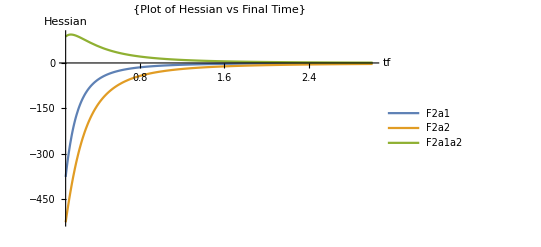

```mathematica
Plot[{hessian[tt][[1,1]],hessian[tt][[2,2]],hessian[tt][[1,2]]},{tt,0.1,3},PlotLabel->{"Plot of Hessian vs Final Time"},PlotLegends->{"F2a1","F2a2","F2a1a2"}, AxesLabel->{"tf","Hessian"}, PlotRange->All]
```

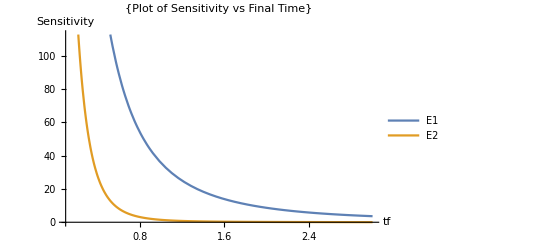

```mathematica
Plot[{Abs[Eigenvalues[hessian[tt]][[1]]],Abs[Eigenvalues[hessian[tt]][[2]]]},{tt,0.1,3},PlotLabel->{"Plot of Sensitivity vs Final Time"},PlotLegends->{"E1","E2"}, AxesLabel->{"tf","Sensitivity"},AxesStyle -> Directive[Black,12]]
```

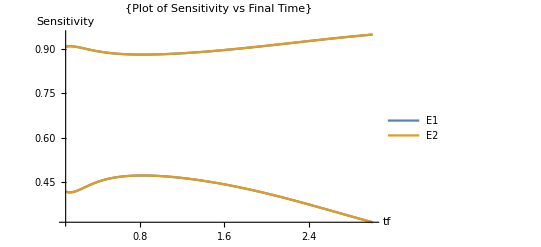

```mathematica
Plot[{Abs[Eigenvectors[hessian[tt]][[1]]],Abs[Eigenvectors[hessian[tt]][[2]]]},{tt,0.1,3},PlotLabel->{"Plot of Sensitivity vs Final Time"},PlotLegends->{"E1","E2"}, AxesLabel->{"tf","Sensitivity"}]
```